94.6402

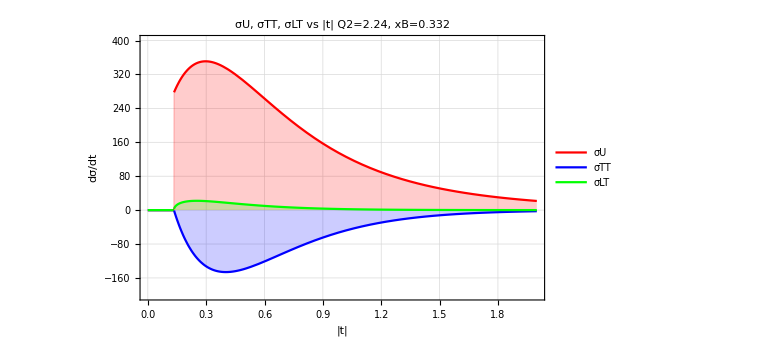

-0.3

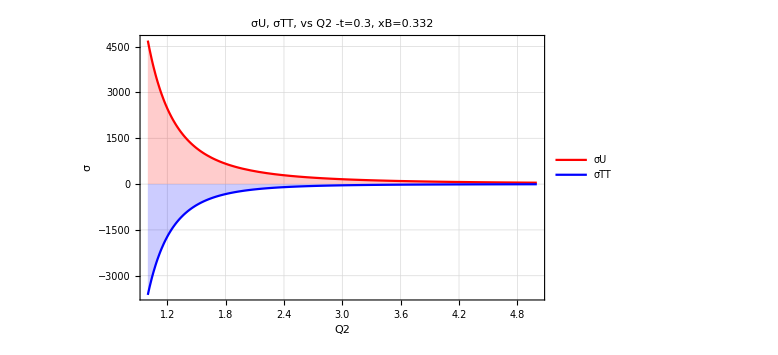

2.24

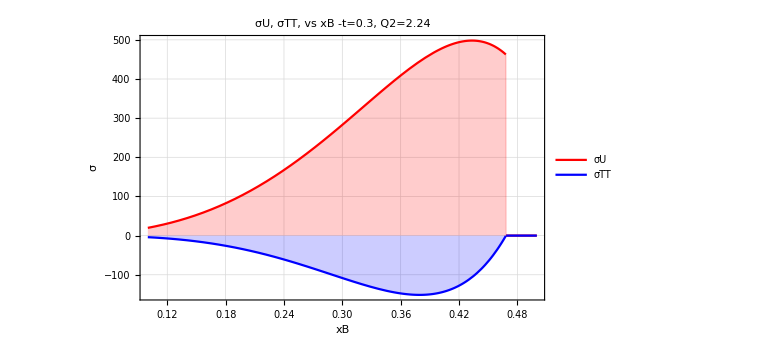

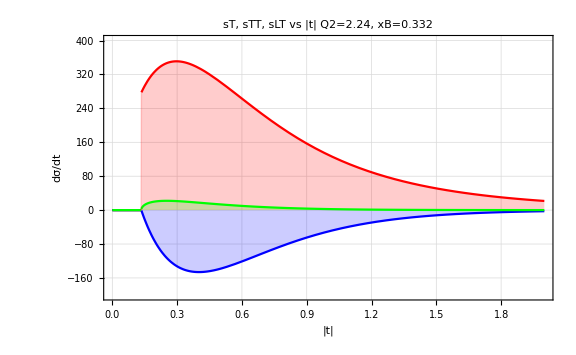

{0.131,0.169,0.186,0.223,0.27,0.313,0.238,0.275,0.332,0.403,0.336,0.423,0.362,0.428,0.496,0.451,0.513,0.539}

{1.14,1.38,1.61,1.75,1.87,1.95,2.1,2.21,2.24,2.34,2.71,2.75,3.12,3.23,3.29,3.68,3.76,4.23}

{235.506,261.468,211.069,266.328,358.789,455.545,183.978,229.182,346.468,447.186,208.549,310.374,168.818,210.573,0.,165.893,0.,0.}

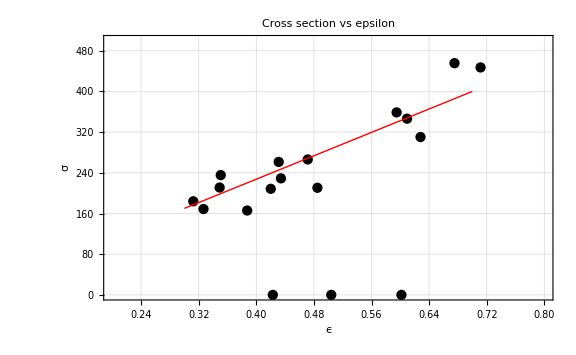

```mathematica
mpi0    = 0.1349764 ;
mp           = 0.93827231 ;
Ebeam      = 5.75;
(*
* 6.2059,0.8019,-0.1064,1.8361,0.00,
* 94.6402,3.4433,-1.9773,-0.1315,0.0000,16.9977,2.1240,
*)
p1=6.2059;
p2=0.8019;
p3=-0.1064;
p4=1.836;
p5=0.0;

p6=94.6402 
p7=3.4433;
p8=-1.9773;
p9=-0.1315;
p10=0.0;
p11=16.9977;
p12=2.1240;

ALPHA=0.00729927;
Hc2=389379.36;
ksi[Q2_,x_]:=x/(2-x)*(1+mp^2/Q2);
W[Q2_,x_]:=Sqrt[Q2*(1/x-1)+mp^2];
E1CM[Q2_,x_]:=(W[Q2,x]^2+Q2+mp^2)/(2*W[Q2,x]);
E3CM[Q2_,x_]:=(W[Q2,x]^2-mpi0^2+mp^2)/(2*W[Q2,x]);
P1CM[Q2_,x_]:= Sqrt[E1CM[Q2,x]^2-mp^2];
P3CM[Q2_,x_]:= Sqrt[E3CM[Q2,x]^2-mp^2];
y[Q2_,x_,E_]:=Q2/(2*mp*x*E);
E1[Q2_,x_,E]:=Q2/(4*E^2);

tmin[Q2_,x_]:=-((Q2+mpi0^2)^2/4/W[Q2,x]^2-(P1CM[Q2,x]-P3CM[Q2,x])^2);
PHASE[Q2_,x_]:=16*Pi*(W[Q2,x]^2-mp^2)*Sqrt[W[Q2,x]^4+Q2^2+mp^4+2*W[Q2,x]^2*Q2-2*W[Q2,x]^2*mp^2+2*Q2*mp^2];
HT[t_,Q2_,x_]:=p1*Exp[(p2+p3*(Log[x]-Log[0.15]))*t]*Q2^(p4/2.);
ET[t_,Q2_,x_]:=p6*Exp[(p7+p8*(Log[x]-Log[0.15]))*t]*Q2^(p9/2.);
HTEBAR[t_,Q2_,x_]:=p11*Exp[p12*t];

sTT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],-Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sT[t_,Q2_,x_]:= If[-t>tmin[Q2,x],    Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sLT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],Hc2*4.*Pi*ALPHA/Sqrt[2.]/PHASE[Q2,x]/Q2^1.5*ksi[Q2,x]*Sqrt[1.-ksi[Q2,x]^2]*Sqrt[-t-tmin[Q2,x]]/2/mp*HTEBAR[t,Q2,x]^2,0.0];
sL[t_,Q2_,x_]:=0.0;
eps1[Q2_,x_,E_]:=(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2));
eps[Q2_,x_,E_]:=If[eps1[Q2,x,E]>0.0,(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2)),0.0];
sU[t_,Q2_,x_,E_]:=sT[t,Q2,x]+eps[Q2,x,E]*sL[t,Q2,x];
(*Plot[{sU[-t,2.,0.2,Ebeam]},{t,0.,2.}]*)
(*----------------------------------------------------*)
Q2List={  1.14,  1.38,   1.61,  1.75,  1.87,   1.95,    2.1,  2.21,   2.24,  2.34,  2.71,  2.75,  3.12,   3.23,   3.29,  3.68,  3.76,4.230};
xBList={ 0.131,0.169,0.186,0.223,0.270,0.313,0.238,0.275,0.332,0.403,0.336,0.423,0.362,0.428,0.496,0.451,0.513,0.539};

(*Q2List={  1.14,  1.38,   1.61,  1.75,  1.87,   1.95,    2.1,  2.21,   2.24,  2.34,  2.71,  2.75,  0.1,0.1,0.1,0.1,0.1,0.1};
xBList={ 0.131,0.169,0.186,0.223,0.270,0.313,0.238,0.275,0.332,0.403,0.336,0.423,  .01,  .01,  .01,  .01,  .01,.01};*)
epsList={
eps[Q2List[[1]],xBList[[1]],Ebeam],eps[Q2List[[2]],xBList[[2]],Ebeam],eps[Q2List[[3]],xBList[[3]],Ebeam],eps[Q2List[[4]],xBList[[4]],Ebeam],eps[Q2List[[5]],xBList[[5]],Ebeam],eps[Q2List[[6]],xBList[[6]],Ebeam],
eps[Q2List[[7]],xBList[[7]],Ebeam],eps[Q2List[[8]],xBList[[8]],Ebeam],eps[Q2List[[9]],xBList[[9]],Ebeam],eps[Q2List[[10]],xBList[[10]],Ebeam],eps[Q2List[[11]],xBList[[11]],Ebeam],eps[Q2List[[12]],xBList[[12]],Ebeam],
eps[Q2List[[13]],xBList[[13]],Ebeam],eps[Q2List[[14]],xBList[[14]],Ebeam],eps[Q2List[[15]],xBList[[15]],Ebeam],eps[Q2List[[16]],xBList[[16]],Ebeam],eps[Q2List[[17]],xBList[[17]],Ebeam],eps[Q2List[[18]],xBList[[18]],Ebeam]
};
T=-0.35;
sTList={
sT[T,Q2List[[1]],xBList[[1]]],sT[T,Q2List[[2]],xBList[[2]]],sT[T,Q2List[[3]],xBList[[3]]],sT[T,Q2List[[4]],xBList[[4]]],sT[T,Q2List[[5]],xBList[[5]]],sT[T,Q2List[[6]],xBList[[6]]],
sT[T,Q2List[[7]],xBList[[7]]],sT[T,Q2List[[8]],xBList[[8]]],sT[T,Q2List[[9]],xBList[[9]]],sT[T,Q2List[[10]],xBList[[10]]],sT[T,Q2List[[11]],xBList[[11]]],sT[T,Q2List[[12]],xBList[[12]]],
sT[T,Q2List[[13]],xBList[[13]]],sT[T,Q2List[[14]],xBList[[14]]],sT[T,Q2List[[15]],xBList[[15]]],sT[T,Q2List[[16]],xBList[[16]]],sT[T,Q2List[[17]],xBList[[17]]],sT[T,Q2List[[18]],xBList[[18]]]
};
(*========  sT, sTT, sLT  ================*) 
Plot[{sT[-t,2.24,.332],sTT[-t,2.24,.332],sLT[-t,2.24,.332]},{t,0.,2.},
PlotLabel->"σU, σTT, σLT vs |t|           Q2=2.24, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"|t|","dσ/dt"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.,2.},{-200,400.}},
PlotLegends->Placed[{"σU","σTT","σLT"},Right]
]
(*----*)
xxB=0.332; tt=-0.3
Plot[{sT[tt,Q2,xxB],sTT[tt,Q2,xxB]},{Q2,1.,5.},
PlotLabel->" σU, σTT, vs Q2          -t=0.3, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"Q2","σ"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{1.,5.},All},
PlotLegends->Placed[{"σU","σTT"},Right]
]
(*----*)
xxB=0.332; tt=-0.3; QQ2=2.24
Plot[{sT[tt,QQ2,xB],sTT[tt,QQ2,xB]},{xB,.1,.5},
PlotLabel->" σU, σTT, vs xB          -t=0.3, Q2=2.24",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"xB","σ"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{.1,.5},All},
PlotLegends->Placed[{"σU","σTT"},Right]
]


Plot[{sT[-t,2.24,.332],sTT[-t,2.24,.332],sLT[-t,2.24,.332]},{t,0.,2.},
PlotLabel->"sT, sTT, sLT vs |t|           Q2=2.24, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"|t|","dσ/dt"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.,2.},{-200,400.}}
]
xBList
Q2List
sTList
(*========  PLOTS  ================*) 
Data=Transpose@{epsList,sTList};
lineStyle={Thick,Red};
line1=Line[{{0.3,170},{0.7,400.}}];
ListPlot[Data,
PlotLabel->"Cross section vs epsilon",
PlotStyle->{Black},
Frame->True,
FrameLabel->{"ϵ","σ"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.2,0.8},{0.,500.}},
Epilog->{Directive[lineStyle],line1}
]
```